# Основные символы и приёмы работы

## Association <||>

Основы

В каком-то смысле это как словарь в Python.

```mathematica
assoc=<|1->6,4->7,36->-3,22->7,40->4|>;
```

```mathematica
assoc[22]
```

7

```mathematica
assoc@f[5]=g[6];
```

```mathematica
assoc
```

<|1→6,4→7,36→-3,22→7,40→4,f[5]→g[6]|>

```mathematica
assoc@f[5]
```

g[6]

```mathematica
<|{1->6,4->7,36->-3,22->7,40->4}|>
```

<|1→6,4→7,36→-3,22→7,40→4|>

```mathematica
Lookup[assoc,123,77]
```

77

```mathematica
If[KeyExistsQ[assoc,123],assoc[123],77]
```

77

```mathematica
1/.assoc
```

6

```mathematica
assoc@6=89;
```

```mathematica
1/.assoc
```

6

```mathematica
assoc@_Integer=x;
```

```mathematica
888888/.assoc
```

888888

Ассоциация может быть автоматически сформирована при применении Association к листу. Не забыть заменить листы на стрелочки.

Чистые функции и ассоциации.

```mathematica
#1+#2&[1,879]
```

880

```mathematica
assoc=<|"a"->2,"b"->ji,"c"->ccc|>;
```

```mathematica
#["a"]&@assoc
```

2

```mathematica
#a&@assoc
```

2

```mathematica
l1={{"y",99},{"o",888},{"u",i[i]}};
```

```mathematica
<|Rule@@@l1|>
```

<|y→99,o→888,u→i[i]|>

Применение

Найти за O(кол-во слагаемых) по времени суммарные коэффициенты при одинаковых f(x,y) с доступом к результату за O(1) по времени.

```mathematica
expr=2(2+a)f[1,2]+(8u-b)f[2,3]-5f[1,2];
```

```mathematica
Collect[expr,f[_,_]]
```

(-5+2 (2+a)) f[1,2]+(-b+8 u) f[2,3]

```mathematica
a-b//FullForm
```

Plus[a,Times[-1,b]]

```mathematica
assoc=<||>;
```

```mathematica
Replace[#,k_ f[a_,b_]:>(
assoc@f[a,b]=Lookup[assoc,f[a,b],0]+k;
)]&/@expr;
```

```mathematica
assoc
```

<|f[1,2]→-5+2 (2+a),f[2,3]→-b+8 u|>

На основе листов и ассоциаций строятся базы данных Dataset.

# Работа с экспериментальными данными

## Аппроксимация данных

Импорт файла:

```mathematica
raw=Import@FileNameJoin@{NotebookDirectory[],"f1.xlsx"}
```

{{{T,sigma,dsigma},{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}}

Вычленение данных:

```mathematica
data=raw⟦1,2;;⟧
```

{{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}

Использование функции Around (появилась в версии 12) для удобной работы с ошибками:

```mathematica
Around[1,0.1]+Around[2,0.1]
```

3.000.14

```mathematica
Around@@@data⟦All,2;;⟧
```

{64.41.5,63.01.5,61.91.5,60.11.4,58.41.4,56.51.4,54.01.3}

```mathematica
dataWithErrors={#1,Around[#2,#3]}&@@@data
```

{{299.6,64.41.5},{305.4,63.01.5},{310.3,61.91.5},{315.3,60.11.4},{320.2,58.41.4},{325.2,56.51.4},{330.,54.01.3}}

Теперь не нужно использовать ErrorBarPlots для отображения ошибок:

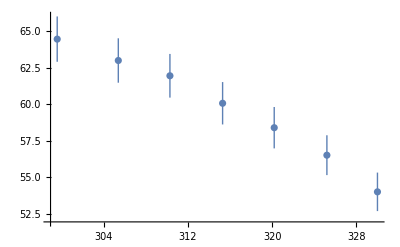

```mathematica
dataAroundPlot=ListPlot@dataWithErrors
```

Также арифметические операции умеют производить математические операции с данными, содержащими ошибки:

Для аппроксимации данных нужно использовать данные без ошибок. Если необходимо учесть ошибки, можно использовать их как веса (опция Weights).

```mathematica
Fit[dataWithErrors,{1,x},x]
```

x -0.340.05+166.17.

```mathematica
fit=LinearModelFit[data⟦All,;;2⟧,{x},x,Weights->(#/Max@#)&[1/data⟦All,3⟧]
]
```

FittedModel[167.139-0.34073 x]

```mathematica
fit@"Properties"
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
fit@"ParameterTable"
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 167.139 | 6.34577 | 26.3386 | 1.47454×10^-6
x | -0.34073 | 0.020091 | -16.9593 | 0.0000130383

У получившегося объекта есть много свойств:

Нормированный квадрат ошибки:

```mathematica
fit@"EstimatedVariance"
```

0.26175

```mathematica
fit@"BestFitParameters"
```

{167.139,-0.34073}

```mathematica
fit@"ParameterErrors"
```

{6.34577,0.020091}

Есть даже исходные данные, по которым производилась аппроксимация:

```mathematica
fit@"Data"
```

{{299.6,64.4413},{305.4,62.9813},{310.3,61.9384},{315.3,60.0612},{320.2,58.3926},{325.2,56.5154},{330.,54.0124}}

Для выражений, не являющихся строкой, объект fit является собственно функцией, получившейся в результате аппроксимации. Построим общий график.

```mathematica
fit["Function"][x]
fit[x]
```

167.139-0.34073 x

167.139-0.34073 x

```mathematica
funcs=fit["MeanPredictionBands",ConfidenceLevel->0.99]
```

{167.139-0.34073 x-4.03214 √(40.2689-0.254857 x+0.00040365 x^2),167.139-0.34073 x+4.03214 √(40.2689-0.254857 x+0.00040365 x^2)}

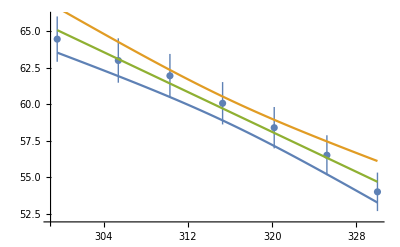

```mathematica
Block[{x},
Show[
dataAroundPlot,
Plot[Evaluate@Append[funcs,fit@x],{x,Sequence@@MinMax@data⟦All,1⟧}]
]
]
```

Небольшой комментарий: с помощью Catch[dataAroundPlot/.(PlotRange→x_):>Throw@x⟦1⟧] можно вычленить реальный диапазон по оси абсцисс из графика dataAroundPlot.

Есть и другие функции для аппроксимации данных, например, Fit, NonlinearModelFit.